```mathematica
S[α_]:=({{1, 0}, {α, 1}}); A=({{0, -ⅈ}, {-ⅈ, 0}}); W[a_]:=({{Exp[a], 0}, {0, Exp[-a]}});(*Stokes, Antistokes and phase operatoes*)
Q[a_,b_,x_]:=Function[z,FullSimplify[(b-a^2/4-D[a,x]/2)/.x->z]];(*From f''+af'+bf==0 to y''+Qy==0*)
U[Q_,g_,x_]:=Function[z,FullSimplify[(Q[g] D[g,x]^2-3/4(D[g,{x,2}]/D[g,x])^2+1/2(D[g,{x,3}]/D[g,x]))/.x->z]];(*From f''+Qf==0 to y''+Uy==0 with variable exchange*)
line[a_,b_]:=Function[t,a+(b-a)t];
```

```mathematica
StokesGraph[Q_,l_]:=
Module[{zeros,zerosColor,poles,polesColor,z,x,y,i,zerosPlot,polesPlot,plotRange,streamPoints,stokes, antistokes},
zerosColor=Blue;
polesColor=Red;

zeros=NSolve[Q[z]==0,z];
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];
zerosPlot=ListPlot[Table[{Re[zeros⟦i⟧],Im[zeros⟦i⟧]},{i,1,Length[zeros]}],PlotStyle->zerosColor];

poles=NSolve[Q[z]^-1==0,z];
poles=Table[z/.poles⟦i⟧,{i,1,Length[poles]}];
polesPlot=ListPlot[Table[{Re[poles⟦i⟧],Im[poles⟦i⟧]},{i,1,Length[poles]}],PlotStyle->polesColor];

plotRange={{Min[Min[Re[zeros]],Min[Re[poles]]]-l,Max[Max[Re[zeros]],Max[Re[poles]]]+l},{Min[Min[Im[zeros]],Min[Im[poles]]]-l,Max[Max[Im[zeros]],Max[Im[poles]]]+l}};
streamPoints=Join[Table[{{Re[zeros⟦i⟧],Im[zeros⟦i⟧]},zerosColor},{i,1,Length[zeros]}],Table[{{Re[poles⟦i⟧],Im[poles⟦i⟧]},polesColor},{i,1,Length[poles]}],{Automatic}];
stokes=StreamPlot[{Sin[-1/2 Arg[Q[x+ⅈ y]]],-Cos[-1/2 Arg[Q[x+ⅈ y]]]},{x,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{y,plotRange⟦2,1⟧,plotRange⟦2,2⟧},StreamPoints->streamPoints,StreamScale->None];
antistokes=StreamPlot[{Cos[-1/2 Arg[Q[x+ⅈ y]]],Sin[-1/2 Arg[Q[x+ⅈ y]]]},{x,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{y,plotRange⟦2,1⟧,plotRange⟦2,2⟧},StreamPoints->streamPoints,StreamScale->None];
{Show[stokes,zerosPlot,polesPlot,ImageSize->Large],Show[antistokes,zerosPlot,polesPlot,ImageSize->Large]}
];
```

```mathematica
sqrt[f_,{x_,start_,a_,b_,end_}]:=
Module[{roots,chunks,cuts,i,t},
roots=NSolve[Im[f[t]]==0&&a<t<b,t]//Quiet;
cuts={start};
For[i=1,i≤Length[roots],i++,
If[Re[f[t/.roots⟦i⟧]]<0,AppendTo[cuts,t/.roots⟦i⟧],];
];
AppendTo[cuts,end];

chunks={};
For[i=2,i≤Length[cuts],i++,
AppendTo[chunks,If[Mod[i,2]==0,{√f[x],cuts⟦i-1⟧<x<cuts⟦i⟧},{-√f[x],cuts⟦i-1⟧<x<cuts⟦i⟧}]];
];

Piecewise[chunks]
];
```

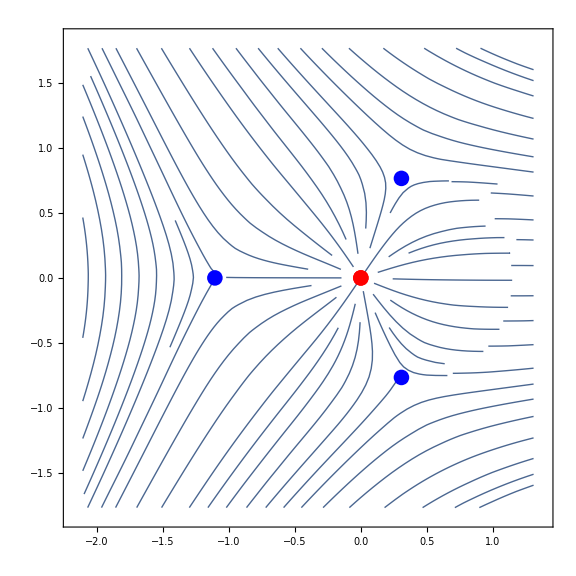
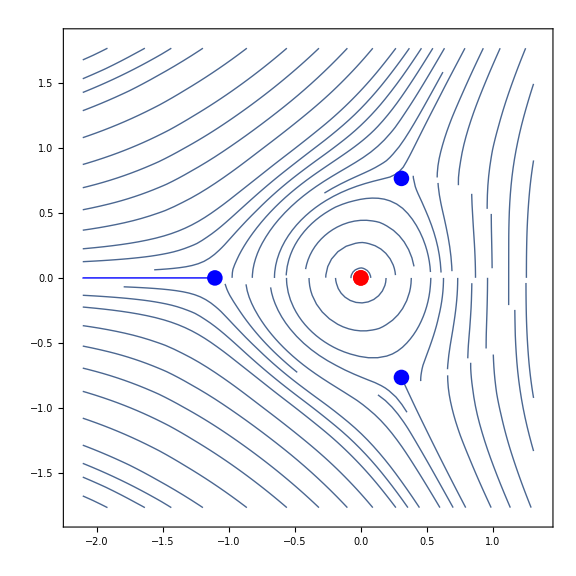

```mathematica
β=0;δ=0.7;
potential=Function[x,-(δ^2+x+3/(4 x^2))];
StokesGraph[potential,1]
Clear[β,δ,potential];
```

```mathematica
S[Subscript[s, 2]].W[f].S[Subscript[s, 1]].({{1}, {0}})//Simplify
```

{{ⅇ^f},{ⅇ^-f s_1+ⅇ^f s_2}}

{-1.38883,0.194416+0.708678 ⅈ,0.194416-0.708678 ⅈ}

0.804431-1.55939 ⅈ

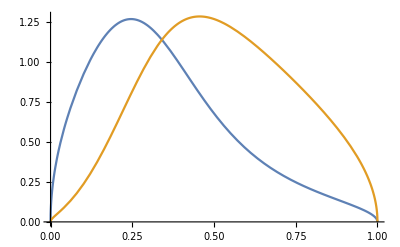
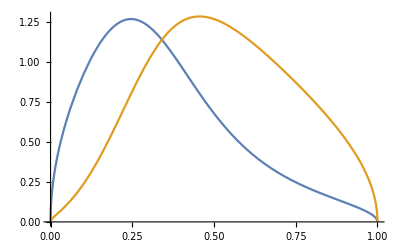

```mathematica
δ=1;
potential=Function[x,-(δ^2+x+3/(4 x^2))];
zeros=NSolve[potential[z]==0,z];
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦3⟧;
b=zeros⟦1⟧;

f=Function[t,potential[line[a,b][t]]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

NIntegrate[-ⅈ (a-b)sqrtf[t],{t,0,1}]
{Plot[{Re[√f[t]],Im[√f[t]]},{t,0,1}],Plot[{Re[sqrtf[t]],Im[sqrtf[t]]},{t,0,1},PlotRange->Full]}

Clear[δ,β,a,b,f,zeros,chunks,sqrtf,potential];
```

```mathematica
(*Constructing ab function for β==0*)
δbegining=-2;δend=2;δnstep=300;IabList={};
potential=Function[{x,δ},-3/(4 x^2)-x-δ^2];
ProgressIndicator[Dynamic[(δ-δbegining)/(δend-δbegining)]]
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,

zeros=NSolve[potential[z,δ]==0,z]//Quiet;

a=z/.zeros⟦3⟧;
b=z/.zeros⟦1⟧;

f=Function[t,potential[line[a,b][t],δ]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

ab=NIntegrate[-ⅈ (a-b)sqrtf[t],{t,0,1}];
AppendTo[IabList,{δ,ab}];

];

IabFunc=Interpolation[IabList];
Clear[δ,a,b,ab,f,chunks,sqrtf,potential,zeros];
```

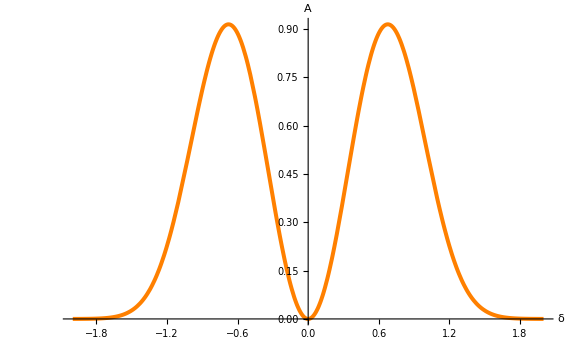

```mathematica
Dissipation={};
begining=-2;end=2;nstep=300;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]

For[δ=begining,δ≤end,δ+=(end-begining)/nstep,

R=ⅇ^(-2 IabFunc[δ]) Subscript[s, 1]+Subscript[s, 2]/.{Subscript[s, 1]->2ⅈ ⅇ^(2IabFunc[0]),Subscript[s, 2]->-ⅈ}//Quiet;
Dissipation=Append[Dissipation,{δ,1-Abs[R]^2}];
]; 
Clear[R,δ(*,a,b,ab,ab0,f,chunks,sqrtf,potential,zeros*)];
(*ListPlot[Dissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"},ImageSize->Large]*)
Plot[Interpolation[Dissipation][x],{x,-2,2},
PlotRange->Full,
AxesLabel->{Style["δ",FontSize->40,Black],Style["A",FontSize->40,Black]},
ImageSize->Large,
LabelStyle->{FontSize->20},
PlotStyle->{Orange,Thickness[0.005]}]
```

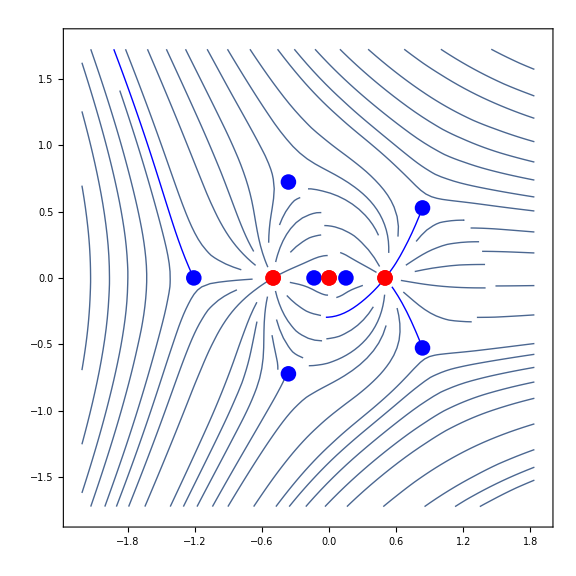
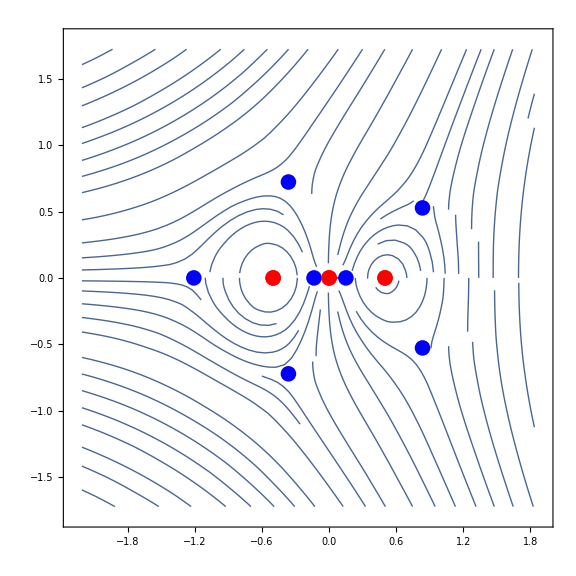

```mathematica
β=0.5;δ=0.5;
potential=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
StokesGraph[potential,1]
Clear[β,δ,potential];
```

{-0.908562,0.454281+0.786834 ⅈ,0.454281-0.786834 ⅈ,-1.64355×10^-11+0.00185216 ⅈ,-1.64355×10^-11-0.00185216 ⅈ,0.000311717,-0.000311717}

-4.85051-0.45345 ⅈ

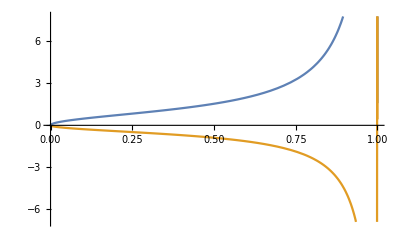
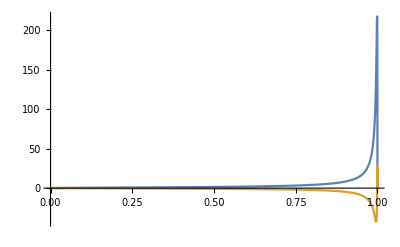

```mathematica
δ=0.001;β=0.001;
potential=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦3⟧;
b=zeros⟦5⟧;

f=Function[t,potential[line[a,b][t]]];
chunks=sqrt[f,{t,0,10^-10,1-10^-10,1}];
sqrtf=Function[t,chunks];

NIntegrate[-ⅈ (a-b)(*√f[t]*)sqrtf[t],{t,0,1}]
{Plot[{Re[√f[t]],Im[√f[t]]},{t,0,1}],Plot[{Re[sqrtf[t]],Im[sqrtf[t]]},{t,0,1},PlotRange->Full]}

Clear[δ,β,a,b,f,zeros,chunks,sqrtf,potential];
```

{-0.908562,0.454281+0.786834 ⅈ,0.454281-0.786834 ⅈ,-1.64355×10^-11+0.00185216 ⅈ,-1.64355×10^-11-0.00185216 ⅈ,0.000311717,-0.000311717}

4.85052-1.36035 ⅈ

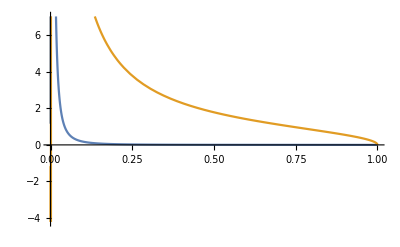
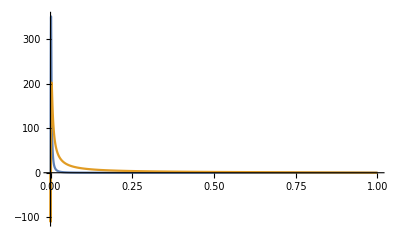

```mathematica
δ=0.001;β=0.001;
potential=Function[x,(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))/(4 (x^3-x β^2)^2)];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

b=zeros⟦5⟧;
c=zeros⟦1⟧;

f=Function[t,potential[line[b,c][t]]];
chunks=sqrt[f,{t,0,10^-10,1-10^-10,1}];
sqrtf=Function[t,chunks];

NIntegrate[-ⅈ (b-c)(*√f[t]*)sqrtf[t],{t,0,1}]
{Plot[{Re[√f[t]],Im[√f[t]]},{t,0,1}],Plot[{Re[sqrtf[t]],Im[sqrtf[t]]},{t,0,1},PlotRange->Full]}

Clear[δ,β,b,c,f,zeros,chunks,sqrtf,potential];
```

```mathematica
(*Constructing ab and bc functions*)
δbegining=-2;δend=2;δnstep=10;
βbegining=10^-2;βend=1;βnstep=10;
abList={};bcList={};
potential=Function[{x,δ,β},1/(4 (x^3-x β^2)^2)(-4 x^7+12 x^5 β^2+β^4-12 x^3 β^4+4 x β^6-4 x^6 δ^2+x^4 (-3+8 β δ (1+β δ))-2 x^2 β^2 (5+2 β δ (2+β δ)))];
ProgressIndicator[Dynamic[(β-βbegining)/(βend-βbegining)]]
For[β=βbegining,β<βend,β+=(βend-βbegining)/βnstep,
For[δ=δbegining,δ<δend,δ+=(δend-δbegining)/δnstep,

zeros=NSolve[potential[z,δ,β]==0,z]//Quiet;

a=z/.zeros⟦3⟧;
b=z/.zeros⟦5⟧;
c=z/.zeros⟦1⟧;

f=Function[t,potential[line[a,b][t],δ,β]];
chunks=sqrt[f,{t,0,10^-10,1-10^-10,1}];
sqrtAB=Function[t,chunks];
ab=NIntegrate[-ⅈ (a-b)sqrtAB[t],{t,0,1}];
AppendTo[abList,{{δ,β},ab}];

f=Function[t,potential[line[b,c][t],δ,β]];
chunks=sqrt[f,{t,0,10^-10,1-10^-10,1}];
sqrtBC=Function[t,chunks];
bc=NIntegrate[-ⅈ (b-c)sqrtBC[t],{t,0,1}];
AppendTo[bcList,{{δ,β},bc}];

];
];

abFunc=Interpolation[abList];
bcFunc=Interpolation[bcList];
Clear[δ,β,a,b,c,ab,bc,sqrtAB,sqrtBC,f,chunks,potential,zeros,abList,bcList];
```

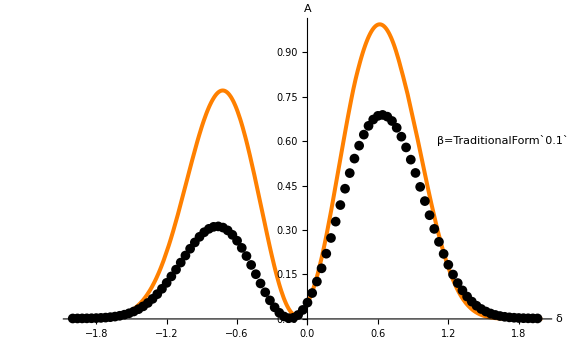

```mathematica
Dissipation={};
begining=-2;end=2;nstep=300;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]
β=0.1;

For[δ=begining,δ<end,δ+=(end-begining)/nstep,
R=ⅇ^(-2 (abFunc[δ,β]+bcFunc[δ,β])) Subscript[s, 1]+ⅇ^(-2 bcFunc[δ,β]) Subscript[s, 2]+Subscript[s, 3]/.{Subscript[s, 1]->-1.8ⅈ,Subscript[s, 2]->0,Subscript[s, 3]->-ⅈ}//Quiet;
Dissipation=Append[Dissipation,{δ,1-Abs[R]^2}];
]; 
Clear[R,δ,β(*,a,b,c,ab,bc,sqrtAB,sqrtBC,f,chunks,potential,zeros*)];
(*ListPlot[Dissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"},ImageSize->Large] *)
Show[Plot[Interpolation[Dissipation][x],{x,-2,2},PlotRange->Full,
AxesLabel->{Style["δ",FontSize->40,Black],Style["A",FontSize->40,Black]},
ImageSize->Large,
LabelStyle->{FontSize->20},
PlotStyle->{Orange,Thickness[0.005]}](*,lowField*)]
```

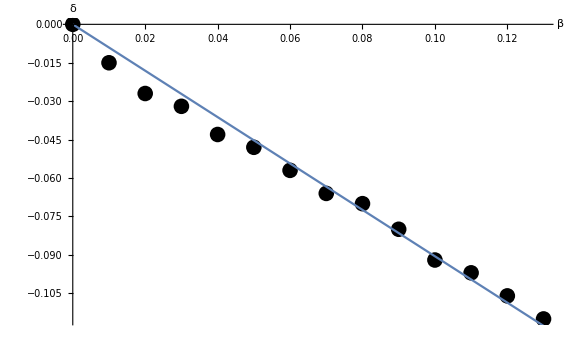

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/others/experiments/exersices/results/eta/zeroDissipationFromAnisortopism[Stokes].csv

/Users/akutlin/Documents/private/VSHOPF/Egor/diplom/wolfram/others/experiments/exersices/results/eta/zeroDissipationFromAnisortopism[Stokes].png

```mathematica
βδStokesMinimum={{0,0},{0.01,-0.015},{0.02,-0.027},{0.03,-0.032},{0.04,-0.043},{0.05,-0.048},{0.06,-0.057},{0.07,-0.066},{0.08,-0.07},{0.09,-0.08},{0.1,-0.092},{0.11,-0.097},{0.12,-0.106},{0.13,-0.115}};

experiment=ListPlot[βδStokesMinimum,PlotRange->Full,AxesLabel->{β,δ},PlotStyle->Black];
fittingFunction=Function[β,a*β];
fit=FindFit[βδStokesMinimum,fittingFunction[β],a,β];
theory=Plot[fittingFunction[β]/.fit,{β,0,0.13},PlotRange->Full,PlotLegends->ToString[fittingFunction[β]/.fit,TraditionalForm]];

result=Show[{experiment,theory},ImageSize->Large]

SaveData["results/eta/zeroDissipationFromAnisortopism[Stokes].csv",βδStokesMinimum,"CSV"]
SaveData["results/eta/zeroDissipationFromAnisortopism[Stokes].png",result,"PNG"]
Clear[experiment,theory,fittingFunction,fit,result];
```

```mathematica
(*
 *
*
*
*
*
*
*
*
*
* Stokes analysis for electrical field; not working; just a memory; RIP!
*
*
*
*
*
*
*
*
*
 *)
```

```mathematica
(*β=0.7;δ=0.5;
potential=Function[x,1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))];
StokesGraph[potential,0.5]
Clear[β,δ,potential];*)
```

```mathematica
(*β=0.1;δ=1.1;
potential=Function[x,1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))];
zeros=NSolve[potential[z]==0,z];
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}]

a=zeros⟦2⟧;
c=zeros⟦1⟧;

f=Function[t,potential[line[a,c][t]]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

NIntegrate[-ⅈ (a-c)sqrtf[t],{t,0,1}]
{Plot[{Re[√f[t]],Im[√f[t]]},{t,0,1}],Plot[{Re[sqrtf[t]],Im[sqrtf[t]]},{t,0,1},PlotRange->Full]}

Clear[δ,β,a,c,f,zeros,chunks,sqrtf,potential];*)
```

```mathematica
(*Dissipation={};
begining=-1;end=1;nstep=100;β=0.1;
ProgressIndicator[Dynamic[(δ-begining)/(end-begining)]]

For[δ=begining,δ≤end,δ+=(end-begining)/nstep,
potential=Function[x,1/4 (1/x^2-4 x+(4 β^2)/x-4 δ^2-3/((x+δ^2)^2)+(2-4 β δ)/(x^2+x δ^2))];
zeros=NSolve[potential[z]==0,z]//Quiet;
zeros=Table[z/.zeros⟦i⟧,{i,1,Length[zeros]}];

a=If[Length[zeros]>3,zeros⟦2⟧,zeros⟦1⟧];
(*b=-δ^2;*)
c=zeros⟦1⟧;

f=Function[t,potential[line[a,c][t]]];
chunks=sqrt[f,{t,0,10^-2,1-10^-2,1}];
sqrtf=Function[t,chunks];

ac=If[a==c,0,NIntegrate[-ⅈ (a-c)sqrtf[t],{t,0,1}]];
(*bc=NIntegrate[-ⅈ (b-c)√(potential[s]/.s->line[b,c][t]),{t,0,1}];*)

R=ⅇ^(-2 (ac)) Subscript[s, 1]+ⅇ^(-2 bc) Subscript[s, 2]+Subscript[s, 3]/.{Subscript[s, 1]->ⅈ,Subscript[s, 2]->0,Subscript[s, 3]->ⅈ};
Dissipation=Append[Dissipation,{δ,1-Abs[R]^2}];
]; 
Clear[R,δ,β,a,b,c,ac,bc,zeros,f,chunks,sqrtf,potential];
ListPlot[Dissipation,PlotRange->Full,AxesLabel->{"δ","dissipation"}]*)
```